```mathematica
nexact[x_,t_,u0_,L_,D_]=4 u0/((1)π)Sin[(1)π/L x] Exp[-D (1)^2 π^2/L^2 t]
```

(4 ⅇ^(-(D π^2 t)/L^2) u0 Sin[(π x)/L])/π

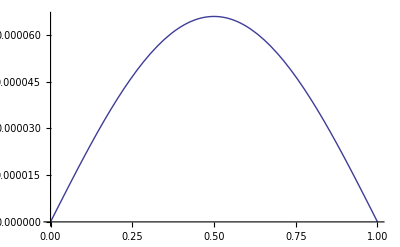

```mathematica
Plot[nexact[x,1,1,1,1],{x,0,1}]
```

```mathematica
nexact2[x_,t_,u0_,L_,D_]=4 Sum[u0/((2n+1)π)Sin[(2 n +1)π/L x] Exp[-D (2n+1)^2 π^2/L^2 t],{n,0,100}];
```

```mathematica
Plot[nexact2[x,1,1,1,1],{x,0,1}]
```

-Graphics-

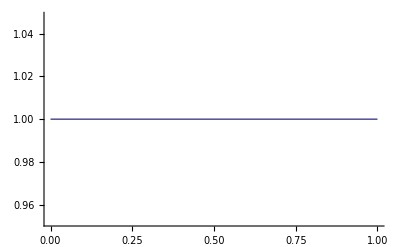

```mathematica
Plot [nexact[x,1,1,1,1]/nexact2[x,1,1,1,1],{x,0,1}]
```

```mathematica
Plot [nexact[x,1,1,1,1]/nexact2[x,1,1,1,1],{x,0,1},PlotRange ->{-0.001, 0.001}]
```

-Graphics-